```mathematica
ClearAll["Global`*"]

wd=SetDirectory@NotebookDirectory[];

styles={Directive[RGBColor[0,0,0],AbsoluteThickness[3.5]],Directive[RGBColor[0.9,0,0],AbsoluteThickness[3],AbsoluteDashing[Medium]],Directive[RGBColor[0,0,1],AbsoluteThickness[3],AbsoluteDashing[{10,5}]],Directive[RGBColor[0,0.5,0],AbsoluteThickness[2],AbsoluteDashing[{10,5,2,5}]],Directive[RGBColor[1,0.5,0.0],AbsoluteThickness[2],AbsoluteDashing[{1,4}]],Directive[RGBColor[0.5,0.5,0.5],AbsoluteThickness[2],AbsoluteDashing[{1,4}]]};

FrameTicksFontSize=16;
FrameFontSize=16;PlotOptions={Axes->False,Frame->True,FrameTicksStyle->{Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Times"],Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Times"]},FrameStyle->{Directive[Black,FontSize->FrameFontSize,FontFamily->"Times",AbsoluteThickness[1]],Directive[Black,FontSize->FrameFontSize,FontFamily->"Times",AbsoluteThickness[1]]},AspectRatio->0.75,ImageSize->Medium,PlotStyle->styles,PlotRange->All};
SetOptions[Plot,PlotOptions];
SetOptions[LogPlot,PlotOptions];
SetOptions[LogLogPlot,PlotOptions];
SetOptions[LogLinearPlot,PlotOptions];
SetOptions[ListPlot,PlotOptions];
SetOptions[PolarPlot,PlotOptions];

Nf=3;
eg=16Pi^2/30;
eq=6*3*7Pi^2/120;  (*check these later*)
sFac = eg+eq ;

rationalPolyFit[data_,NN_,MM_]:=Module[{a,b,varsa,varsb,vars,sol,varsc,varsd,Q},
varsa=Table[a[n],{n,0,NN}];
varsb=Table[b[m],{m,0,MM}];
vars=Join[varsa,varsb];
sol=FindFit[data,Sum[a[n]x^n,{n,0,NN}]/Sum[b[m]x^m,{m,0,MM}],vars,x,MaxIterations->1000];
varsc=varsa/.sol;
varsd=varsb/.sol;
Return[Sum[varsc[[n+1]]x^n,{n,0,NN}]/Sum[varsd[[m+1]]x^m,{m,0,MM}]];
];
```

```mathematica
eosDataRaw=Import[wd<>"/eos.dat"];
eosData= Take[eosDataRaw,{3,Length[eosDataRaw]}];
(* Subscript[ϵ, eq](T) *)
LogEDLogTInt = Interpolation[eosData[[All,{1,2}]]];
e[T_] = 10^LogEDLogTInt[Log[10,T]];
(* Subscript[P, eq](T) *)
LogPLogTInt = Interpolation[eosData[[All,{1,4}]]];
P[T_] = 10^LogPLogTInt[Log[10,T]];
(* Subscript[c, s]^2(T) *)
LogdPLogEdInt = Interpolation[eosData[[All,{2,5}]]];
dPIntE[e_]=10^LogdPLogEdInt[Log[10,e]];
LogdELogEdInt = Interpolation[eosData[[All,{2,3}]]];
dEIntE[e_]=10^LogdELogEdInt[Log[10,e]];
cs2[T_] = dPIntE[e[T]]/dEIntE[e[T]];

eosDataRaw2=Import[wd<>"/best.dat"];
temp = 0.005067731*eosDataRaw2[[1;;450,2]];
```

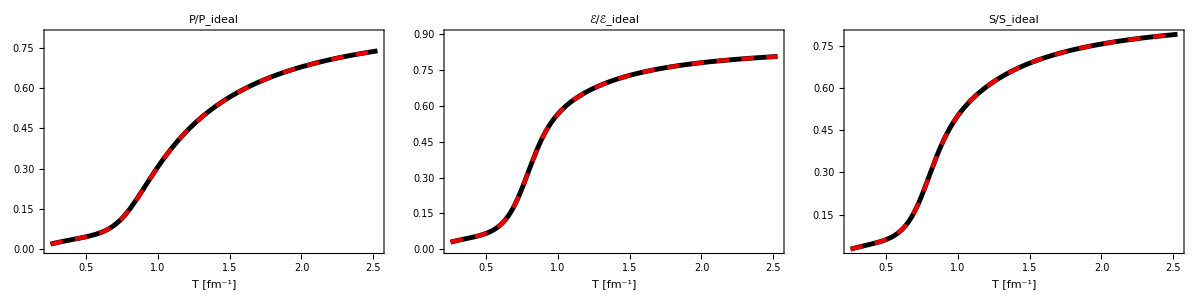

```mathematica
Tmin = temp[[1]];
Tmax=temp[[450]];

S[T_]=P'[T];
S2[T_]=(e[T]+P[T])/T;

emin=efit[Tmin];
emax=efit[Tmax];

Grid[{{Plot[{P[T]/(sFac T^4/3),P[T]/(sFac T^4/3)},{T,Tmin,Tmax},PlotRange->{0,0.8},PlotStyle->styles,PlotLabel->Style["P/P_ideal",FontSize->20],ImageSize->320,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],

Plot[{e[T]/(sFac T^4),e[T]/(sFac T^4)},{T,Tmin,Tmax},PlotRange->{0,0.9},PlotStyle->styles,PlotLabel->Style["ℰ/ℰ_ideal",FontSize->20],ImageSize->320,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],

Plot[{S[T]/(4.0/3.0*sFac T^3),S2[T]/(4.0/3.0*sFac T^3)},{T,Tmin,Tmax},PlotStyle->styles,PlotLabel->Style["S/S_ideal",FontSize->20],ImageSize->320,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]
```

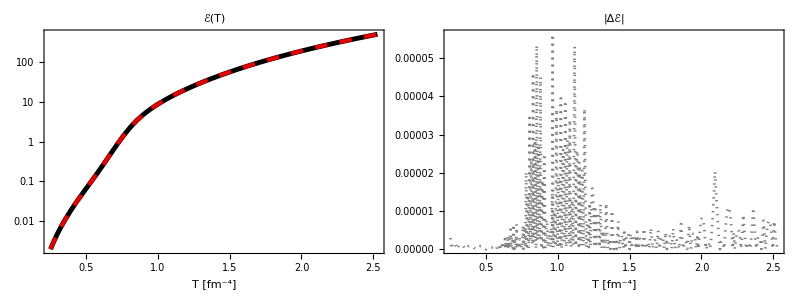

(-0.6746595680417311 + 15.18004717055557*T - 150.28838666045098*Power(T,2) + 856.8728238453558*Power(T,3) - 3067.006874419056*Power(T,4) + 
     6887.691793468362*Power(T,5) - 8689.01204393483*Power(T,6) + 2779.5133034548844*Power(T,7) + 7527.143247800599*Power(T,8) - 
     7280.007098663352*Power(T,9) - 5948.659144649617*Power(T,10) + 9517.34072428892*Power(T,11) + 5432.293784982603*Power(T,12) - 
     11518.267479577982*Power(T,13) - 3662.4391070118304*Power(T,14) + 11510.3287888067*Power(T,15) + 2190.1375458702637*Power(T,16) - 
     14631.511315975464*Power(T,17) + 11753.561347532514*Power(T,18) - 4063.357489150804*Power(T,19) + 541.1883866332131*Power(T,20))/
   (-25.236559574714622 + 171.3985969608387*T - 470.68935437785206*Power(T,2) + 609.039379929916*Power(T,3) - 254.62577340009915*Power(T,4) - 
     161.54720638956582*Power(T,5) + 41.634863182950326*Power(T,6) + 95.77801093178024*Power(T,7) + 271.26565801570024*Power(T,8) - 
     228.11450258806724*Power(T,9) - 549.2377700940492*Power(T,10) + 558.3772963304361*Power(T,11) + 620.0220147386352*Power(T,12) - 
     1369.1552177484705*Power(T,13) + 960.5451160750602*Power(T,14) - 299.88416268160154*Power(T,15) + 24.60448576154993*Power(T,16) + 
     7.327185654554338*Power(T,17) - 1.6962229435786575*Power(T,18) + 0.20830329719464258*Power(T,19) - 0.01095197778233111*Power(T,20))

```mathematica
(*** e(T) ***)

edata=Table[{temp[[i]],e[temp[[i]]]},{i,1,Length[temp]}];

n =20;

efit[T_]=rationalPolyFit[edata,n,n]/.{x->T};

Grid[{{
LogPlot[{e[T],efit[T]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["ℰ(T)",FontSize->20],Axes->False,FrameLabel->{"T [fm^-4]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],

Plot[{Abs[e[T]-efit[T]]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["|Δℰ|",FontSize->20],Axes->False,FrameLabel->{"T [fm^-4]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]
CForm[efit[T]]
```

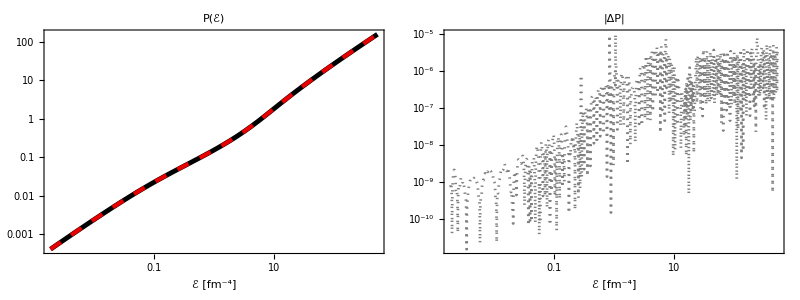

(5.075564888183663e-8 - 0.0000562169058017086*e - 0.22264079778393814*Power(e,2) - 96.54111777097086*Power(e,3) - 
     1756.4940900442318*Power(e,4) - 3839.550980182813*Power(e,5) + 43314.75256472724*Power(e,6) + 21484.684622349*Power(e,7) - 
     130046.39756226703*Power(e,8) + 31055.12603591556*Power(e,9) + 39710.876799090234*Power(e,10) - 1699.2739439957898*Power(e,11) + 
     457.07148223707463*Power(e,12) - 2.6124197272811243*Power(e,13) - 10.644483495536646*Power(e,14) + 0.9338976604508398*Power(e,15) - 
     0.08154575247701629*Power(e,16) + 0.007945758495188623*Power(e,17) - 0.00032112712608626663*Power(e,18) + 
     1.3849387546528496e-6*Power(e,19) + 1.0319807626964377e-7*Power(e,20) + 2.4411168029716984e-10*Power(e,21) - 
     5.320369073003463e-14*Power(e,22))/
   (-0.00014387478025277176 - 1.1792584683886174*e - 389.6323718241302*Power(e,2) - 6977.840105310985*Power(e,3) - 
     30423.03772874304*Power(e,4) + 172511.16609332536*Power(e,5) + 395148.28097748733*Power(e,6) - 927429.602347526*Power(e,7) - 
     1969.7658108555734*Power(e,8) + 442307.7633162228*Power(e,9) - 61081.643776514844*Power(e,10) + 10031.861047012935*Power(e,11) - 
     1004.1267102196177*Power(e,12) + 34.34877412677497*Power(e,13) - 1.1282071952740738*Power(e,14) - 0.03273759822023652*Power(e,15) + 
     0.020818561379492638*Power(e,16) - 0.0011806678144587483*Power(e,17) + 9.452128098430316e-6*Power(e,18) + 
     3.5138214637099674e-7*Power(e,19) + 7.566271511306246e-10*Power(e,20) - 1.7260152864418335e-13*Power(e,21) + 
     2.3271917596080208e-18*Power(e,22))

```mathematica
(*** P(e) ***)

Pdata=Table[{efit[temp[[i]]],P[temp[[i]]]},{i,1,Length[temp]}];
Pfunc=Interpolation[Pdata];

n =22;

Pfit[e_]=rationalPolyFit[Pdata,n,n]/.{x->e};

Grid[{{
LogLogPlot[{Pfunc[e],Pfit[e]},{e,emin,emax},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["P(ℰ)",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],

LogLogPlot[{Abs[Pfunc[e]-Pfit[e]]},{e,emin,emax},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["|ΔP|",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]
CForm[Pfit[e]]
```

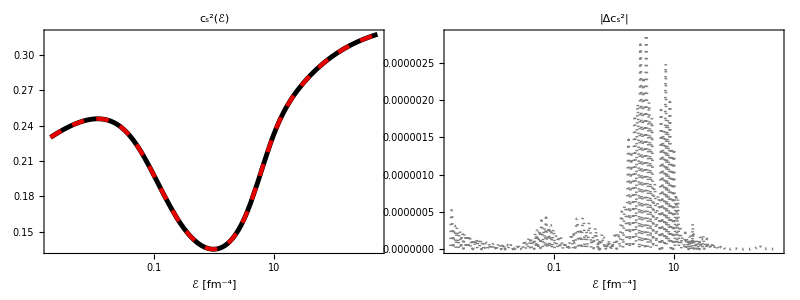

(-2.178802623232077e-8 - 0.000028058668053969316*e + 0.0707167841389791*Power(e,2) + 30.072115831801668*Power(e,3) + 
     2235.4049904745293*Power(e,4) + 41418.70672195756*Power(e,5) + 358508.8110784304*Power(e,6) + 1.1590875075390663e6*Power(e,7) + 
     954248.3211844995*Power(e,8) - 50721.294467359*Power(e,9) + 16465.82334234105*Power(e,10) - 908.4548567500927*Power(e,11) - 
     252.7359144972058*Power(e,12) + 53.91419969140143*Power(e,13) - 12.026262562371759*Power(e,14) + 1.6556097635897582*Power(e,15) - 
     0.11488691302515308*Power(e,16) + 0.003829345418196134*Power(e,17) - 0.000041174256263276295*Power(e,18) - 
     6.534667798749817e-7*Power(e,19) + 1.251380387174281e-8*Power(e,20) + 4.584558932434191e-11*Power(e,21) + 
     1.7120085646159452e-14*Power(e,22))/
   (-1.2153701643802135e-7 - 0.00008294478323975135*e + 0.3175076406677123*Power(e,2) + 120.51666836485872*Power(e,3) + 
     8774.085137082211*Power(e,4) + 182446.2005223917*Power(e,5) + 1.995089196043474e6*Power(e,6) + 9.161741300187482e6*Power(e,7) + 
     8.731822712749625e6*Power(e,8) - 2.156494891121747e6*Power(e,9) + 482885.5410394763*Power(e,10) - 69411.77018853552*Power(e,11) + 
     6760.932013473378*Power(e,12) - 510.63270233261545*Power(e,13) + 8.175727094657239*Power(e,14) + 3.248437668454592*Power(e,15) - 
     0.32487966107613314*Power(e,16) + 0.012482882608729243*Power(e,17) - 0.00015856500475657135*Power(e,18) - 
     1.7681600567702772e-6*Power(e,19) + 4.075596322495956e-8*Power(e,20) + 1.4197025154850574e-10*Power(e,21) + 
     5.1982187467659597e-14*Power(e,22))

```mathematica
(*** Subscript[c, s]^2(e) ***)


(*Subscript[c, s]^2 = dp/de = dp/dT dT/de = s dT/de= (e+p)/(T de/dT)*)

cs2data=Table[{e[temp[[i]]],cs2[temp[[i]]]},{i,1,Length[temp]}];

cs2func=Interpolation[cs2data];

n =22;

cs2fit[e_]=rationalPolyFit[cs2data,n,n]/.{x->e};


Grid[{{
LogLinearPlot[{cs2func[e],cs2fit[e]},{e,emin,emax},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["c_s^2(ℰ)",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],

LogLinearPlot[{Abs[cs2func[e]-cs2fit[e]]},{e,emin,emax},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["|Δc_s^2|",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]

CForm[cs2fit[e]]
```

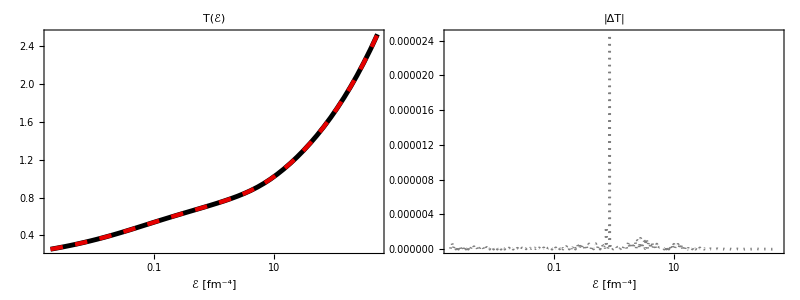

(2.805869997121848e-7 + 0.0016687441079320283*e + 1.4839310262134133*Power(e,2) + 328.65797655737566*Power(e,3) + 
     20588.110903563724*Power(e,4) + 333446.5800069805*Power(e,5) + 697363.6527955428*Power(e,6) - 1.726106947423048e6*Power(e,7) - 
     1.4534822597460109e6*Power(e,8) + 1.6041416532072239e6*Power(e,9) + 647591.4839233705*Power(e,10) + 196069.7894032533*Power(e,11) - 
     16477.03273134262*Power(e,12) + 2239.163501912496*Power(e,13) - 139.4471798412599*Power(e,14) - 56.177945728815814*Power(e,15) + 
     6.286896403438542*Power(e,16) - 0.12504404549704667*Power(e,17) - 0.005436655511967141*Power(e,18) + 0.00012779108537184535*Power(e,19) + 
     1.6538755980411776e-6*Power(e,20) + 3.4758922647083855e-9*Power(e,21) + 1.1123123823913987e-12*Power(e,22))/
   (2.068456663176566e-6 + 0.008270169005048402*e + 5.525127318169887*Power(e,2) + 946.7751657179253*Power(e,3) + 
     45753.72453554468*Power(e,4) + 551625.3416059491*Power(e,5) + 797512.3880244014*Power(e,6) - 2.73675388935463e6*Power(e,7) - 
     1.4424551842244035e6*Power(e,8) + 2.257817112071547e6*Power(e,9) + 747469.0482756988*Power(e,10) + 222730.76660418292*Power(e,11) - 
     30716.511863420095*Power(e,12) + 4901.037822665323*Power(e,13) - 575.9147472089788*Power(e,14) - 14.771489098529415*Power(e,15) + 
     4.999666623329036*Power(e,16) - 0.17506789169898215*Power(e,17) - 0.0018686576242234758*Power(e,18) + 0.00009965134321146708*Power(e,19) + 
     7.777887562653655e-7*Power(e,20) + 1.0812709087693346e-9*Power(e,21) + 1.8461582296389239e-13*Power(e,22))

```mathematica
(*** T(e) ***)

Tdata=Table[{e[temp[[i]]],temp[[i]]},{i,1,Length[temp]}];

Tfunc=Interpolation[Tdata];

n =22;

Tfit[e_]=rationalPolyFit[Tdata,n,n]/.{x->e};

Grid[{{
LogLinearPlot[{Tfunc[e],Tfit[e]},{e,emin,emax},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["T(ℰ)",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->14},AspectRatio->0.75],

LogLinearPlot[{Abs[Tfunc[e]-Tfit[e]]},{e,emin,emax},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["|ΔT|",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->14},AspectRatio->0.75]}}]

CForm[Tfit[e]]
```

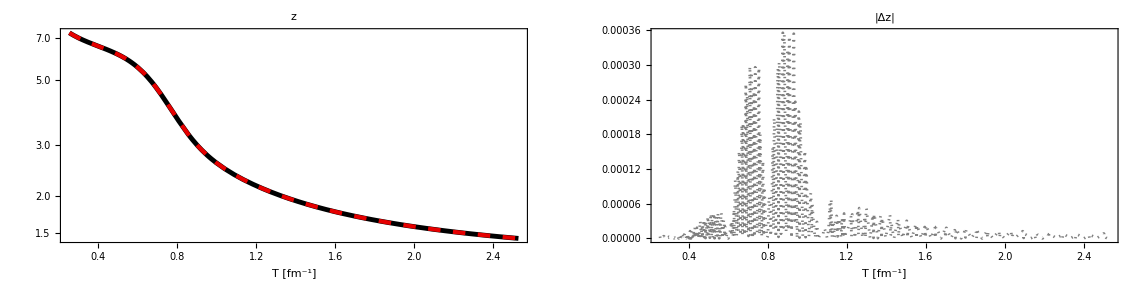

(0.09170766362432285 + 31.477893867949994*T - 171.4720923041977*Power(T,2) + 348.0505433081136*Power(T,3) - 278.01508474473576*Power(T,4) - 
     4.090099452538992*Power(T,5) + 69.51455657407085*Power(T,6) + 57.572779749854725*Power(T,7) - 14.887082827580162*Power(T,8) - 
     61.65146999493058*Power(T,9) - 13.081983675373781*Power(T,10) + 38.32427558472125*Power(T,11) + 17.159335415770617*Power(T,12) - 
     20.356371374162403*Power(T,13) - 14.437661706680801*Power(T,14) + 24.046217260682386*Power(T,15) + 18.24949542696214*Power(T,16) - 
     33.837725550993*Power(T,17) - 25.73947128017313*Power(T,18) + 46.25407785818272*Power(T,19) - 1.3014208236011469*Power(T,20) - 
     17.86161727824165*Power(T,21) + 5.995299077737301*Power(T,22))/
   (-0.2029627504235254 + 5.955678944772665*T - 26.14385042172914*Power(T,2) + 37.910032843493795*Power(T,3) + 12.89477746020681*Power(T,4) - 
     99.75427327035554*Power(T,5) + 98.48666295844663*Power(T,6) + 9.217026288266831*Power(T,7) - 71.2407321036052*Power(T,8) + 
     6.23448005926286*Power(T,9) + 53.36649722702714*Power(T,10) + 1.894894203426874*Power(T,11) - 41.43766327605702*Power(T,12) - 
     18.439061197583815*Power(T,13) + 25.12987742471087*Power(T,14) + 29.06484792258054*Power(T,15) - 4.674554626090905*Power(T,16) - 
     25.34321247283328*Power(T,17) - 11.06682311125567*Power(T,18) + 14.537948966360654*Power(T,19) + 20.210157950158084*Power(T,20) - 
     22.377274103422923*Power(T,21) + 5.77910353680565*Power(T,22))

```mathematica
(*** z(T) ***)

nc = 3.0;
nf = 3.0;
g =Pi^4/180.0*(4.0*(nc^2-1.0)+7.0*nc*nf);
F[T_]=(2.0*Pi^2)/g*S[T]/T^3;

zQuasi=Table[{temp[[i]],""},{i,1,Length[temp]}];
zQuasi[[Length[zQuasi],2]]=x/.FindRoot[x^3*BesselK[3,x]==F[temp[[450]]],{x,1.3},MaxIterations->5000];

For[i = Length[zQuasi]-1, i >0,i--,
zQuasi[[i,2]]=x/.FindRoot[x^3*BesselK[3,x]==F[zQuasi[[i,1]]],{x,zQuasi[[i+1,2]]},MaxIterations->5000];
]

zQuasifunc=Interpolation[zQuasi];
zQuasidata=Table[{T,zQuasifunc[T]},{T,Tmin,Tmax, 0.005067731}];

n = 22;

zQuasifit[T_]=rationalPolyFit[zQuasidata,n,n]/.{x->T};

GraphicsGrid[{{
LogPlot[{zQuasifunc[T],zQuasifit[T]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["z",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[zQuasifunc[T]-zQuasifit[T]]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["|Δz|",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],}}]

zQuasifit[T]//CForm
```

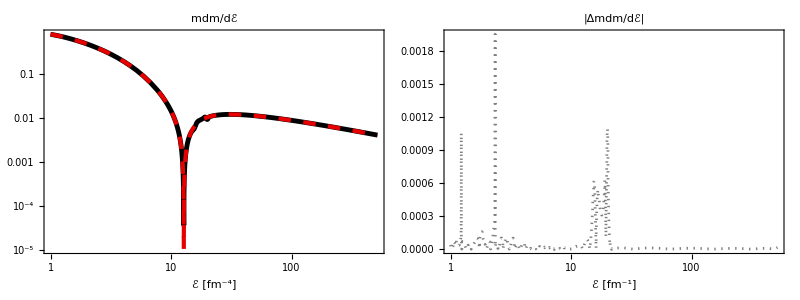

(1.95329061017391e-8 - 3.3864591099208037e-7*e - 0.010132734695886053*Power(e,2) + 1.6753243797332422*Power(e,3) + 
     505.0230978675841*Power(e,4) + 11677.208913547789*Power(e,5) - 55703.604828668744*Power(e,6) + 1479.0200007231247*Power(e,7) + 
     61761.447490081344*Power(e,8) + 143627.25733808105*Power(e,9) + 226690.4925520967*Power(e,10) - 293050.8720934472*Power(e,11) - 
     94524.55168666519*Power(e,12) - 61017.68288638332*Power(e,13) - 229443.3864504896*Power(e,14) + 180361.8519145171*Power(e,15) + 
     243634.70610154347*Power(e,16) - 159284.78192644802*Power(e,17) + 21245.39044520998*Power(e,18) - 1076.649585647334*Power(e,19) + 
     81.46116084351611*Power(e,20) - 8.452263332922929*Power(e,21) + 0.2891561651312173*Power(e,22) + 0.00010477110249757475*Power(e,23) - 
     5.924454664628676e-7*Power(e,24))/
   (1.263748595093237e-11 + 5.369270863996899e-8*e - 0.000031466506506184786*Power(e,2) - 0.009205496057306299*Power(e,3) + 
     4.121377887104778*Power(e,4) + 433.1622186125416*Power(e,5) + 6370.443724035817*Power(e,6) + 38796.78488518795*Power(e,7) - 
     100233.238972959*Power(e,8) + 69521.1493253967*Power(e,9) - 572164.8929417476*Power(e,10) + 695111.7298044853*Power(e,11) - 
     607486.3603072201*Power(e,12) + 647957.760858581*Power(e,13) + 154931.63752634017*Power(e,14) - 407878.1511277599*Power(e,15) + 
     318788.79614717636*Power(e,16) - 403925.1609669887*Power(e,17) + 195835.5382324677*Power(e,18) - 37733.36512024303*Power(e,19) + 
     5990.489285897725*Power(e,20) - 507.5085020546778*Power(e,21) + 12.709293209963018*Power(e,22) + 0.18803526530907066*Power(e,23) - 
     0.0002519337243322702*Power(e,24))

```mathematica
(*** m(e) and dm/de ***) 

mdata=Table[{e[temp[[i]]],temp[[i]]*zQuasifit[temp[[i]]]},{i,1,Length[temp]}];

mfunc=Interpolation[mdata];

mdmde[e_]=mfunc[e]*mfunc'[e];

mdmdedata=Table[{e[temp[[i]]],mdmde[e[temp[[i]]]]},{i,1,Length[temp]}];

n =24;

mdmdefit[e_]=rationalPolyFit[mdmdedata,n,n]/.{x->e};

Grid[{{LogLogPlot[{Abs[mdmde[e]],Abs[mdmdefit[e]]},{e,1.0,emax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["mdm/dℰ",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
LogLinearPlot[{Abs[mdmde[e]-mdmdefit[e]]},{e,1.0,emax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["|Δmdm/dℰ|",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]

mdmdefit[e]//CForm
```

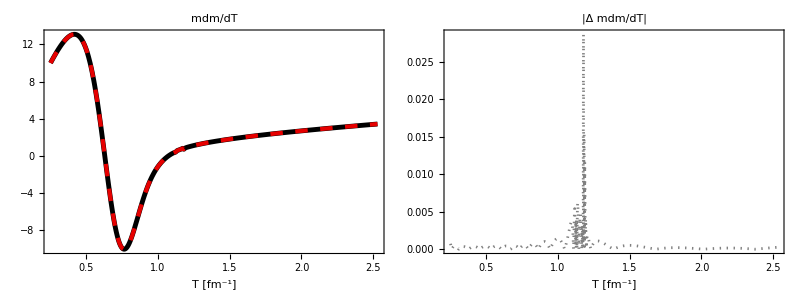

(-3.028163612386263 + 98.73401869758305*T - 511.80174808391024*Power(T,2) + 1055.0741832198837*Power(T,3) - 846.746417261978*Power(T,4) - 
     110.30561292661812*Power(T,5) + 397.43649852839525*Power(T,6) + 149.73095985304266*Power(T,7) - 190.09344913083802*Power(T,8) - 
     185.27871805472296*Power(T,9) + 41.42701637225608*Power(T,10) + 199.19717383158633*Power(T,11) + 24.17109944589548*Power(T,12) - 
     225.5221602242409*Power(T,13) + 41.118417163779505*Power(T,14) + 172.29042730398783*Power(T,15) - 102.18896578757689*Power(T,16) - 
     76.7720473291614*Power(T,17) + 117.24436583720603*Power(T,18) - 53.45778874409243*Power(T,19) + 8.770783901630884*Power(T,20))/
   (0.8206250128057959 - 0.4164311946445899*T - 15.883545739669731*Power(T,2) + 34.49470094656446*Power(T,3) + 69.33570333148452*Power(T,4) - 
     382.55981003290265*Power(T,5) + 612.1392812015968*Power(T,6) - 333.37199795398413*Power(T,7) - 221.07178216721667*Power(T,8) + 
     329.2271693848648*Power(T,9) + 57.438161620880535*Power(T,10) - 238.2487820559714*Power(T,11) - 9.292954213897902*Power(T,12) + 
     172.7836083273217*Power(T,13) - 31.044612393751912*Power(T,14) - 96.06511391366193*Power(T,15) + 54.81464315308174*Power(T,16) + 
     4.809677278559935*Power(T,17) - 8.646938417696239*Power(T,18) + 0.1881364321986544*Power(T,19) + 0.5503683342350166*Power(T,20))

```mathematica
(*** m dm/dT ***) 

mQuasifunc[T_] =T*zQuasifit[T]; 

mdmdTQuasi[T_] = mQuasifunc[T] *D[ mQuasifunc[T],T];

mdmdTQuasidata=Table[{temp[[i]],mdmdTQuasi[temp[[i]]]},{i,1,Length[temp]}];

n = 20;

mdmdTQuasifit[T_]=rationalPolyFit[mdmdTQuasidata,n,n]/.{x->T};
Grid[{{
Plot[{mdmdTQuasi[T],mdmdTQuasifit[T]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["mdm/dT",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[mdmdTQuasi[T]-mdmdTQuasifit[T]]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["|Δ mdm/dT|",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]

mdmdTQuasifit[T]//CForm
```

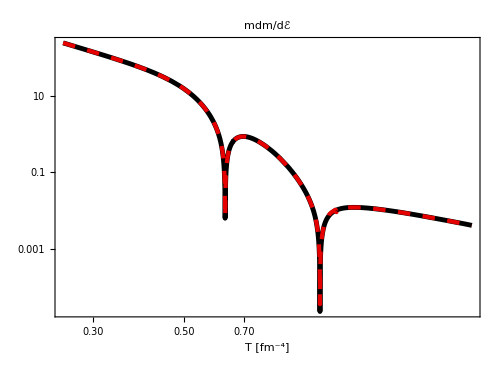

```mathematica
(*** check chain rule in relation: dm/de = cs2/s dm/dT ***)

LogLogPlot[{Abs[mdmdefit[efit[T]]],Abs[cs2fit[efit[T]]/S[T]*mdmdTQuasifit[T]]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->500,Frame->True,PlotLabel->Style["mdm/dℰ",FontSize->24],Axes->False,FrameLabel->{"T [fm^-4]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]
```

-12.9473

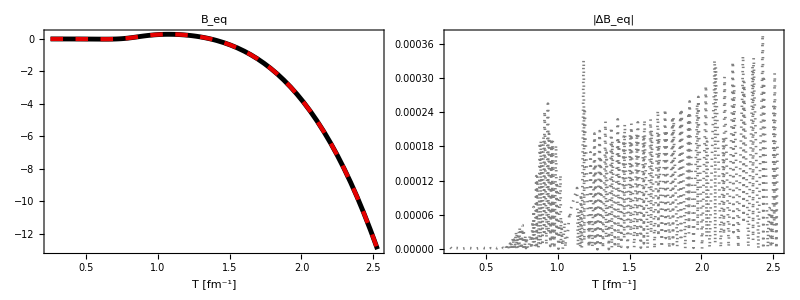

(19.40792947323188 - 342.0263387469813*T + 2578.242086743804*Power(T,2) - 10619.929493490272*Power(T,3) + 24985.83034443322*Power(T,4) - 
     32422.095136126005*Power(T,5) + 20631.134901306315*Power(T,6) - 9226.280024763879*Power(T,7) + 14807.369870741783*Power(T,8) - 
     2888.3379582824937*Power(T,9) - 29195.318316647674*Power(T,10) + 14671.8936104707*Power(T,11) + 33946.737465802296*Power(T,12) - 
     31656.730028637397*Power(T,13) - 4964.959699285339*Power(T,14) + 10877.8429393955*Power(T,15) + 1436.4665900587586*Power(T,16) - 
     2649.0569522213736*Power(T,17) - 610.3672174408359*Power(T,18) + 755.1701409806524*Power(T,19) - 133.9584939041013*Power(T,20))/
   (19142.656974668585 - 154846.05101852873*T + 539267.185191327*Power(T,2) - 1.0215562949639153e6*Power(T,3) + 
     1.0541671057321753e6*Power(T,4) - 393173.65077612136*Power(T,5) - 344907.32542035833*Power(T,6) + 486863.54785741604*Power(T,7) - 
     194270.00402842*Power(T,8) - 28603.417269431873*Power(T,9) + 56129.67324026361*Power(T,10) - 16375.781761169725*Power(T,11) - 
     7598.880720560649*Power(T,12) + 7007.200455460863*Power(T,13) + 330.54710937412455*Power(T,14) - 3505.431547985612*Power(T,15) + 
     3130.5297967162674*Power(T,16) - 1600.0066738078033*Power(T,17) + 469.7385200718001*Power(T,18) - 72.04743960804596*Power(T,19) + 
     4.597612981223469*Power(T,20))

```mathematica
(*** Subscript[B, eq](T) alternative ***)

n = 20;
Pquasi[T_]=(g*T^4)/(2.0*Pi^2)*zQuasifunc[T]^2*BesselK[2,zQuasifunc[T]];

B0Quasi2=Table[{temp[[i]],Pquasi[temp[[i]]]-P[temp[[i]]]},{i,1,Length[temp]}];

B0Quasifunc2=Interpolation[B0Quasi2];

B0Quasifit2[T_]=rationalPolyFit[B0Quasi2,n,n]/.{x->T};

B0Quasifit2[temp[[450]]]

Grid[{{
Plot[{B0Quasifunc2[T],B0Quasifit2[T]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["B_eq",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[B0Quasifunc2[T]-B0Quasifit2[T]]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["|ΔB_eq|",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]

B0Quasifit2[T]//CForm

(* It's probably more accurate to calculate B this way *)
```

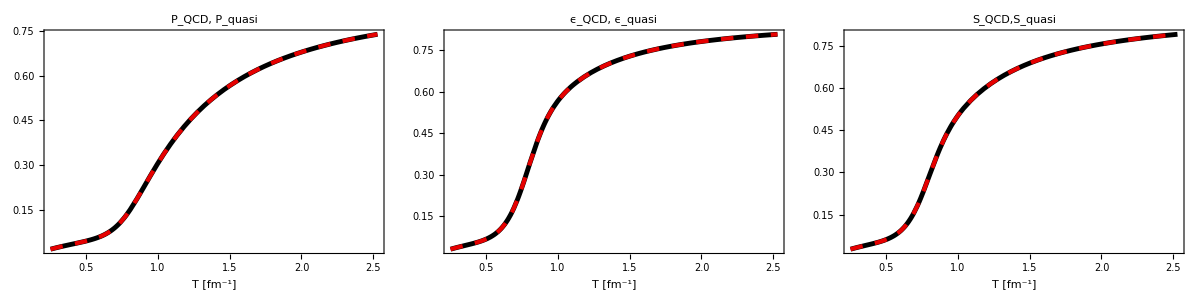

```mathematica
Pquasi[T_]=(g*T^4)/(2.0*Pi^2)*zQuasifunc[T]^2*BesselK[2,zQuasifunc[T]] -B0Quasifunc2[T];
Equasi[T_]=(g*T^4)/(2.0*Pi^2)*zQuasifunc[T]^2*(3.0*BesselK[2,zQuasifunc[T]]+zQuasifunc[T]*BesselK[1,zQuasifunc[T]])+B0Quasifunc2[T];

SQuasi[T_]=(Pquasi[T]+Equasi[T])/T;

Grid[{{Plot[{P[T]/(sFac T^4/3),Pquasi[T]/(sFac T^4/3)},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},PlotLabel->"P_QCD, P_quasi",BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{e[T]/(sFac T^4),Equasi[T]/(sFac T^4)},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},PlotLabel->"ϵ_QCD, ϵ_quasi",BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{S[T]/(4*sFac*T^3/3),SQuasi[T]/(4*sFac*T^3/3)},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},PlotLabel->"S_QCD,S_quasi",BaseStyle->{FontSize->16},AspectRatio->0.75]}}]
```

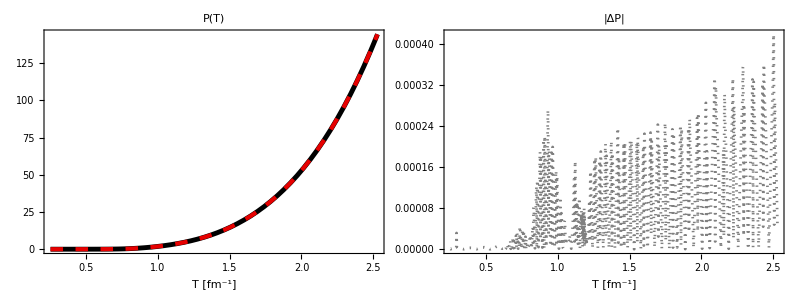

(-0.8914549103919248 + 22.893757617543578*T - 262.75853318435344*Power(T,2) + 1774.3319033783685*Power(T,3) - 7785.941416373705*Power(T,4) + 
     22987.58545677857*Power(T,5) - 45027.79177363824*Power(T,6) + 52611.91278046044*Power(T,7) - 17408.57578517054*Power(T,8) - 
     50285.45807317768*Power(T,9) + 86756.80430610973*Power(T,10) - 48526.419773410766*Power(T,11) - 19311.967677222812*Power(T,12) + 
     42662.78439869659*Power(T,13) - 17448.827470929493*Power(T,14) - 7762.984305727031*Power(T,15) + 10479.701011089866*Power(T,16) - 
     4048.6360628164325*Power(T,17) + 574.2449956937297*Power(T,18))/
   (-65.93242571950124 + 653.4768127891859*T - 2552.5311494461407*Power(T,2) + 4775.39114349216*Power(T,3) - 2840.749736406899*Power(T,4) - 
     5692.808333734398*Power(T,5) + 13351.444318844557*Power(T,6) - 9404.456148503814*Power(T,7) - 4061.1306462544862*Power(T,8) + 
     13945.826080790304*Power(T,9) - 14140.37193397386*Power(T,10) + 9827.411984075683*Power(T,11) - 6161.356026816977*Power(T,12) + 
     3547.6386315042155*Power(T,13) - 1563.8902413865521*Power(T,14) + 455.5517084525443*Power(T,15) - 81.99893845743132*Power(T,16) + 
     8.934040881028778*Power(T,17) - 0.4457653989639154*Power(T,18))

```mathematica
(* Fitting the quasiparticle kinetic pressure (B = 0) *)
Pquasi[T_]=(g*T^4)/(2.0*Pi^2)*zQuasifunc[T]^2*BesselK[2,zQuasifunc[T]];  (*kinetic only; no bag term*)
Pquasidata=Table[{temp[[i]],Pquasi[temp[[i]]]},{i,1,Length[temp]}];
n = 18;
Pquasifit[T_]=rationalPolyFit[Pquasidata,n,n]/.{x->T};

Grid[{{
Plot[{Pquasi[T],Pquasifit[T]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["P(T)",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[Pquasi[T]-Pquasifit[T]]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["|ΔP|",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]
Pquasifit[T]//CForm
```

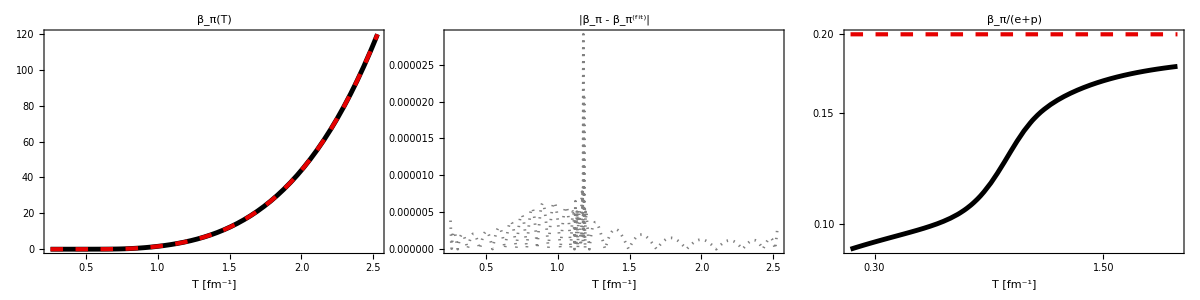

(3.8849752086912623 - 81.75711548883612*T + 758.6855793464125*Power(T,2) - 4080.0043988595335*Power(T,3) + 13998.196317295955*Power(T,4) - 
     31510.132744708902*Power(T,5) + 45243.06190393971*Power(T,6) - 35235.3406336028*Power(T,7) + 177.91096020599664*Power(T,8) + 
     29147.604245677583*Power(T,9) - 25312.14305681918*Power(T,10) + 36.10028178319713*Power(T,11) + 17115.132549366466*Power(T,12) - 
     16732.697486754332*Power(T,13) + 8789.832705192895*Power(T,14) - 2701.796835519705*Power(T,15) + 383.5056919121435*Power(T,16))/
   (177.6960254757862 - 869.2969326874477*T + 1319.1268753523589*Power(T,2) + 404.40956148532797*Power(T,3) - 3172.2287967031607*Power(T,4) + 
     1651.5674255087415*Power(T,5) + 5021.62669182579*Power(T,6) - 9028.791696042206*Power(T,7) + 4970.041353891375*Power(T,8) + 
     2231.4303081440057*Power(T,9) - 5594.563514770515*Power(T,10) + 4487.194614133707*Power(T,11) - 2135.863031817189*Power(T,12) + 
     645.6924363953377*Power(T,13) - 120.68220509406726*Power(T,14) + 13.330024063412038*Power(T,15) - 0.6622117410668655*Power(T,16))

119.764

```mathematica
betapiDataRaw=Import[wd<>"/betapiplotWB.dat"];
betapiData= Take[betapiDataRaw,{2,Length[betapiDataRaw]}];
betapi = Interpolation[betapiData[[All,{1,2}]]];
n = 16;
betapifit[T_]=rationalPolyFit[betapiData,n,n]/.{x->T};
betapiconformal[T_]=0.2*S[T]*T;

Grid[{{Plot[{betapi[T],betapifit[T]},{T,temp[[1]],temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,PlotLabel->Style["β_π(T)",FontSize->24],FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[betapi[T]-betapifit[T]]},{T,Tmin,temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,PlotLabel->Style["|β_π - β_π^(fit)|",FontSize->24],FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
LogLogPlot[{betapi[T]/(T*S[T]),betapiconformal[T]/(T*S[T])},{T,Tmin,temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,PlotLabel->Style["β_π/(e+p)",FontSize->24],FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]
betapifit[T]//CForm
```

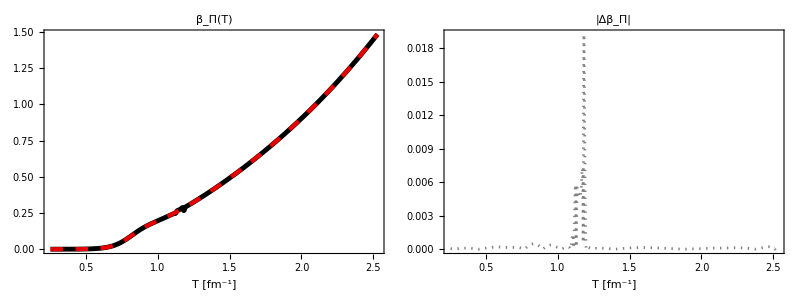

(0.008510670056129977 - 1.353919995523633*T + 13.608904166522786*Power(T,2) - 51.321537229771266*Power(T,3) + 73.96045299666834*Power(T,4) + 
     43.35307088459302*Power(T,5) - 305.47155148480124*Power(T,6) + 456.6456107250134*Power(T,7) - 333.5507775553348*Power(T,8) + 121.29147704125069*Power(T,9) - 
     17.1556447046427*Power(T,10))/
   (189.30433417113048 - 1007.7250064961569*T + 2157.938044817338*Power(T,2) - 2186.1853677466547*Power(T,3) + 680.4998075037523*Power(T,4) + 
     632.8823616536517*Power(T,5) - 590.085899407071*Power(T,6) + 50.80375306281021*Power(T,7) + 109.62729069676597*Power(T,8) - 40.81865517144528*Power(T,9) + 
     3.833720025887098*Power(T,10))

```mathematica
(* betabulk =5.0*betapi/3.0-cs2*(e+p)+cs2*mdmdT*I11 *)

Clear[betabulk,betabulkData,betabulkfit,I11DataRaw,I11Data,I11]

I11DataRaw=Import[wd<>"/betabulkplotWB.dat"];
I11Data= Take[I11DataRaw,{2,Length[I11DataRaw]}];
I11 = Interpolation[I11Data[[All,{1,2}]]];

betabulk[T_]=5.0/3.0*betapi[T]+cs2[T]*(mdmdTQuasifit[T]*I11[T]-(e[T]+P[T]));

betabulkData=Table[{temp[[i]],betabulk[temp[[i]]]},{i,1,Length[temp]}];
betabulk=Interpolation[betabulkData];

n = 10;
betabulkfit[T_]=rationalPolyFit[betabulkData,n,n]/.{x->T};

Grid[{{
Plot[{betabulk[T],betabulkfit[T]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["β_Π(T)",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[betabulk[T]-betabulkfit[T]]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["|Δβ_Π|",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]

betabulkfit[T]//CForm
```